```mathematica
binomial[z_,k_]:=binomial[z,k]=Product[z-j,{j,0,k-1}]/k!
zetaHurwitz[n_,s_,y_,0]:=UnitStep[n-1]
zetaHurwitz[n_,s_,y_,1]:=zetaHurwitz[n,s,y,1]=HarmonicNumber[Floor[n],s]-HarmonicNumber[y,s]
zetaHurwitz[n_,s_,y_,2]:=zetaHurwitz[n,s,y,2]=Sum[(m^(-2s))+2(m^-s) (zetaHurwitz[Floor[n/m],s,m,1]),{m,y+1,Floor[n^(1/2)]}]
zetaHurwitz[n_,s_,y_,k_]:=zetaHurwitz[n,s,y,k]=Sum[(m^(-s k))+k(m^(-s(k-1))) zetaHurwitz[Floor[n/(m^(k-1))],s,m,1]+Sum[binomial[k,j] (m^-s)^j zetaHurwitz[Floor[n/(m^j)],s,m,k-j],{j,1,k-2}],{m,y+1,Floor[n^(1/k)]}]

zeta[n_,s_,1]:=Expand@Sum[binomial[1,k]zetaHurwitz[n,s,1,k],{k,0,1}]
zeta[n_,s_,z_]:=Expand@Sum[binomial[z,k]zetaHurwitz[n,s,1,k],{k,0,Log2@n}]

ka[n_]:=ka[n]=FullSimplify[MangoldtLambda[n]/Log[n]]
```

```mathematica
zeta[200,N@ZetaZero@1,1]
```

-0.42408+0.907121 ⅈ

Infinity::indet: Indeterminate expression (9.21686×10^-6 - 0.0303604\ ⅈ) + -∞ + ∞ encountered.

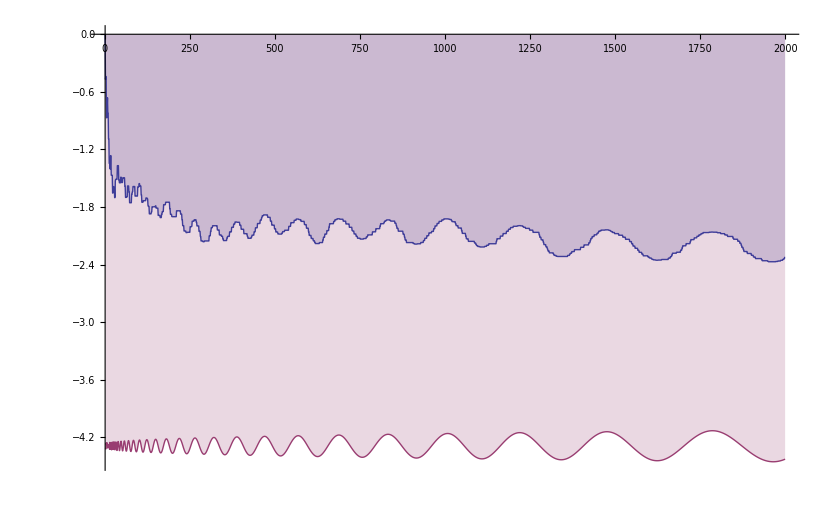

```mathematica
DiscretePlot[{Re[D[zeta[n,.01+N@ZetaZero@5,z],z]/.z->0],Re[Log[Zeta[.01+N@ZetaZero@5]]+ppp[n,.01+N@ZetaZero@5]]},{n,1,2000}]
```

```mathematica
Log[Zeta[1+4.I]]
```

-0.38203+0.080295 ⅈ

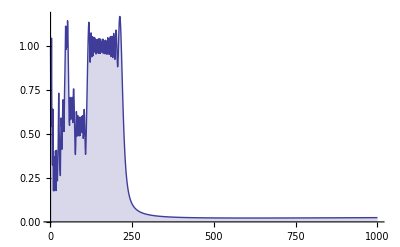

```mathematica
DiscretePlot[Abs[HarmonicNumber[n,N@ZetaZero@1000]],{n,1,1000}]
```

```mathematica
ppp[n_,s_]:=-Gamma[0,(s-1)Log[n]]+Gamma[0,s Log[n]]+Log[s/(s-1)]
```

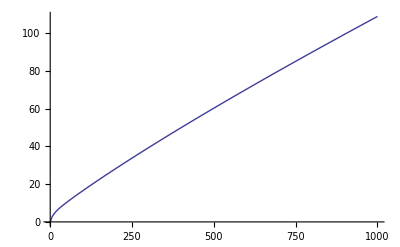

```mathematica
Plot[Abs[ppp[n,1.I]],{n,1,1000}]
```

```mathematica
Log[Zeta[ZetaZero@1]]
```

-∞